```mathematica
(*fmass={0.51,0,105.66,0,1776.99,0,2.3,4.8,1275.,95.,173210.,4180.}*1*10^-3;*)
(*fmass={0.511,0,105.66,0,1776.99,0,1.9,4.4,1320.,87.,173500.,4240.}*1*10^-3;*)
fmass={0.511,0,105.66,0,1776.99,0,3,7,1200.,120.,174000.,4300.}*1*10^-3;
mv={80.42,91.19};
mh=125.09;
thetaW=28.76*π/180;
sw2=Sin[thetaW]^2;
ga={-0.5,0.5,-0.5,0.5,-0.5,0.5,0.5,-0.5,0.5,-0.5,0.5,-0.5};
gv={0.5,-0.5+2*sw2,0.5,-0.5+2*sw2,0.5,-0.5+2*sw2,0.5-4*sw2/3.,-0.5+2*sw2/3.,0.5-4*sw2/3.,-0.5+2*sw2/3.,0.5-4*sw2/3.,-0.5+2*sw2/3.};
Nc={1,1,1,1,1,1,3,3,3,3,3,3};
gs=1.214 ;
v=246;
alphas=gs^2/(4.*π) ;
GF=1.16*10^-5;
(*g2=8*mv[[1]]^2/(√2)*GF;*)
ge=0.302822;
gw=0.6295;
gz=0.7180;
PMNS=0.5Transpose[{{0.799+0.844,0.242+0.494,0.284+0.521},{0.516+0.582,0.467+0.678,0.490+0.695},{0.141+0.156,0.639+0.774,0.615+0.754}}];
CKM=Transpose[{{0.97,0.22,0.0087},{0.22,0.97,0.04},{0.0035,0.041,0.999}}];
Mp=2.4*10^18;
GeV2sec=6.6*10^-25;
kappa=1./Mp ;
DMMass1=Table[i,{i,1,1000,1}];
DMMass2=Table[i,{i,10^3,10^6,10^3}];
DMMass=Catenate[{DMMass1,DMMass2}];
(*DMMass=Table[i,{i,10^3,10^6,10^4}];*)
cota1=4*10^16;
cota2=1*10^23;
Print[Length[DMMass]]
xh[m_]:=mh^2/m^2
xw[m_]:=mv[[1]]^2/m^2
xz[m_]:=mv[[2]]^2/m^2
xf[m_]:=fmass^2/m^2
λ[x_,y_,z_]:=(1-2*(x+y)/z+(x-y)^2/z^2)^(1/2)
p12[s_,m1_,m2_]:=(s-m1^2-m2^2)/2
p13[s_,θ3_,m_,m1_,m2_,m3_]:=1/4(((m^2-s-m3^2)(s+m1^2-m2^2))/s+m^2*λ[m1^2,m2^2,s]*λ[s,m3^2,m^2]*Cos[θ3])
p23[s_,θ12_,m_,m1_,m2_,m3_]:=1/4(((m^2-s-m3^2)(s+m2^2-m1^2))/s-m^2*λ[m1^2,m2^2,s]*λ[s,m3^2,m^2]*Cos[θ12])
Φ[s_,m_,m1_,m2_,m3_]:=(2π)^2/(8^2(2π)^5)λ[m1^2,m2^2,s]*λ[s,m3^2,m^2]
dqqg[s_,m_,m1_,m2_,m3_,ξ_]:=12*9(ξ^2 Mp^2 kappa^4)/(2m)8*gs^2*(p12[s,m1,m2]+2 m1^2)*Φ[s,m,m1,m2,m3]
dffxw[s_,θ12_,θ3_,m_,m1_,m2_,m3_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(2m)gw^2*(p12[s,m1,m2]+2/m3^2 p13[s,θ3,m,m1,m2,m3]*p23[s,θ12,m,m1,m2,m3])*Φ[s,m,m1,m2,m3]
gp[i_]:=ga[[i]]^2+gv[[i]]^2
gm[i_]:=gv[[i]]^2-ga[[i]]^2
dffxz[s_,θ12_,θ3_,m_,m1_,m2_,m3_,i_,ξ_]:=Nc[[i]]*(ξ^2 Mp^2 kappa^4)/(2m)*4/m3^2 gz^2(3*gm[i]*m1*m2*m3^2+gp[i]*m3^2 p12[s,m1,m2]+2p13[s,θ3,m,m1,m2,m3]*p23[s,θ12,m,m1,m2,m3])*Φ[s,m,m1,m2,m3]
Φ2[s12_,s34_,m_,m1_,m2_,m3_,m4_]:=(4π)^3/(8^3(2π)^8)λ[s12,s34,m^2]λ[m1^2,m2^2,s12]λ[m3^2,m4^2,s34]
dhhww[s12_,s34_,m_,m1_,m2_,m3_,m4_,ξ_]:=1(ξ^2 Mp^2 kappa^4)/(2m*v^4)(2*mv[[1]]^4+((s34-2 mv[[1]]^2)/2)^2)*Φ2[s12,s34,m,m1,m2,m3,m4]
dhhzz[s12_,s34_,m_,m1_,m2_,m3_,m4_,ξ_]:=1/4(ξ^2 Mp^2 kappa^4)/(2m*v^4)(2*mv[[2]]^4+((s34-2 mv[[2]]^2)/2)^2)*Φ2[s12,s34,m,m1,m2,m3,m4]
Gamma1=Table[0,{i,1,Length[DMMass]}];
Gamma2=Table[0,{i,1,Length[DMMass]}];
Gamma3=Table[0,{i,1,Length[DMMass]}];
Gamma4=Table[0,{i,1,Length[DMMass]}];
Gamma5=Table[0,{i,1,Length[DMMass]}];
Gamma6=Table[0,{i,1,Length[DMMass]}];
Gamma7=Table[0,{i,1,Length[DMMass]}];
Gamma8=Table[0,{i,1,Length[DMMass]}];
Gamma9=Table[0,{i,1,Length[DMMass]}];
qqg[m_,m1_,m2_,m3_,ξ_]:=NIntegrate[dqqg[s,m,m1,m2,m3,ξ],{s,(m1+m2)^2,(m-m3)^2}]
ffxw[m_,m1_,m2_,m3_,ξ_]:=NIntegrate[dffxw[s,θ12,θ3,m,m1,m2,m3,ξ],{s,(m1+m2)^2,(m-m3)^2},{θ12,0,π},{θ3,0,π}]
ffxz[m_,m1_,m2_,m3_,i_,ξ_]:=NIntegrate[dffxz[s,θ12,θ3,m,m1,m2,m3,i,ξ],{s,(m1+m2)^2,(m-m3)^2},{θ12,0,π},{θ3,0,π}]
hhww[m_,m1_,m2_,m3_,m4_,ξ_]:=NIntegrate[dhhww[s12,s34,m,m1,m2,m3,m4,ξ],{s12,(m1+m2)^2,(m-m3-m4)^2},{s34,(m3+m4)^2,(m-√s12)^2},AccuracyGoal->20]
hhzz[m_,m1_,m2_,m3_,m4_,ξ_]:=NIntegrate[dhhzz[s12,s34,m,m1,m2,m3,m4,ξ],{s12,(m1+m2)^2,(m-m3-m4)^2},{s34,(m3+m4)^2,(m-√s12)^2},AccuracyGoal->20]
hh[m_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(32π)m^3(1+2*xh[m])^2(1-4*xh[m])^(1/2)
zz[m_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(32π)m^3(1-4*xz[m]+12*xz[m]^2)*(1-4*xz[m])^(1/2)
ww[m_,ξ_]:=(ξ^2 Mp^2 kappa^4)/(16π)m^3(1-4*xw[m]+12*xw[m]^2)*(1-4*xw[m])^(1/2)
ffx[m_,m1_,i_,ξ_]:=Nc[[i]](ξ^2 Mp^2 kappa^4)/(8π)m*m1^2(1-4*m1^2/m^2)^(3/2)
```

2000

```mathematica
ξ=1;
For[i=1,i<=Length[DMMass],i++,{
m=DMMass[[i]];

If[m>2*mh,Gamma1[[i]]=hh[m,ξ]];

If[m>2*mv[[2]],Gamma2[[i]]=zz[m,ξ]];

If[m>2*mv[[1]],Gamma3[[i]]=ww[m,ξ]];

For[ii=1,ii<13,ii++,{
If[m>2*fmass[[ii]],Gamma4[[i]]+=ffx[m,fmass[[ii]],ii,ξ]]}];

For[ii=7,ii<13,ii++,{
	If[m>2*fmass[[ii]],Gamma5[[i]]+=qqg[m,fmass[[ii]],0,fmass[[ii]],ξ]]}];

For[ii=0,ii<3,ii++,{
For[jj=0, jj<3, jj++,{
	If[m>fmass[[2*ii+7]]+fmass[[2*jj+8]]+mv[[1]],Gamma6[[i]]+=3*ffxw[m,fmass[[2*ii+7]],fmass[[2*jj+8]],mv[[1]],ξ]*(CKM[[ii+1]][[jj+1]])^2]}];}]

For[ii=0,ii<3,ii++,{
For[jj=0, jj<3, jj++,{
	If[m>fmass[[2*ii+1]]+fmass[[2*jj+2]]+mv[[1]],Gamma6[[i]]+=ffxw[m,fmass[[2*ii+1]],fmass[[2*jj+2]],mv[[1]],ξ]*(PMNS[[ii+1]][[jj+1]])^2]}];}]

For[ii=1,ii<13,ii++,{
	If[m>2*fmass[[ii]]+mv[[2]],Gamma7[[i]]+=ffxz[m,fmass[[ii]],fmass[[ii]],mv[[2]],ii,ξ]]}];

If[m>2*mh+2*mv[[1]],Gamma8[[i]]=hhww[m,mh,mh,mv[[1]],mv[[1]],ξ]];

If[m>2*mh+2*mv[[2]],Gamma9[[i]]=hhzz[m,mh,mh,mv[[2]],mv[[2]],ξ]];

}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Gammatot=Gamma1+Gamma2+Gamma3+Gamma4+Gamma5+Gamma6+Gamma7+Gamma8+Gamma9;
```

```mathematica
BR1=Table[{DMMass[[i]],Gamma1[[i]]/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR2=Table[{DMMass[[i]],(Gamma2[[i]]+Gamma3[[i]])/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR4=Table[{DMMass[[i]],Gamma4[[i]]/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR5=Table[{DMMass[[i]],Gamma5[[i]]/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR6=Table[{DMMass[[i]],(Gamma6[[i]]+Gamma7[[i]])/Gammatot[[i]]},{i,1,Length[DMMass]}];
BR7=Table[{DMMass[[i]],(Gamma8[[i]]+Gamma9[[i]])/Gammatot[[i]]},{i,1,Length[DMMass]}];
Life=Table[{DMMass[[i]],GeV2sec/Gammatot[[i]]},{i,1,Length[DMMass]}];
Cons1=Table[{DMMass[[i]],cota1},{i,1,Length[DMMass]}];
Cons2=Table[{DMMass[[i]],cota2},{i,1,Length[DMMass]}];
```

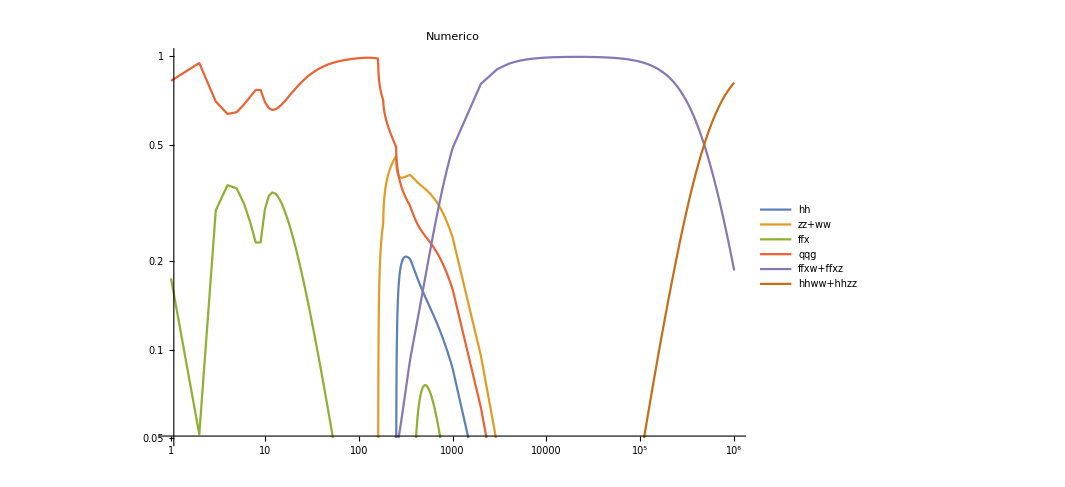

```mathematica
ListLogLogPlot[{BR1,BR2,BR4,BR5,BR6,BR7},ImageSize->Large,PlotLegends->Placed[{"hh","zz+ww","ffx","qqg","ffxw+ffxz","hhww+hhzz"},{0.7,0.75}],Joined->True,GridLines->{{1,2,3,5,10,50,100,500,1000,10^4,10^5,10^6}, {0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}},PlotRange->{{1,10^6},{0.05,1}},PlotLabel->"Numerico"]
```

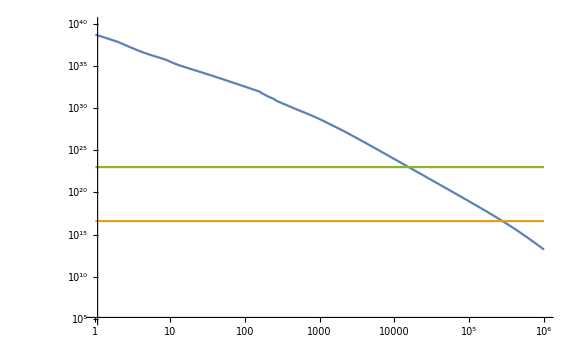

```mathematica
ListLogLogPlot[{Life,Cons1,Cons2},ImageSize->Large,Joined->True,PlotRange->{{1,10^6},{10^5,10^40}}]
```